zR[λ,w0] is the Rayleigh length of the beam. This corresponds to the distance it takes for the cross section area of the beam to double.
	w0 is the waist of the beam at its focus.
	λ is the wavelength of light (or wavelength / index of refraction if measuring in a medium)
w [λ,w0,z,z0] is the radius of the beam at a distance of (z - z0) from the waist
	z is the distance of where you are measuring from a reference point
	z0 is the distance of the waist from the same reference point
II[λ,I0,w0,x,y,z,z0] is the intensity profile of the beam
By default the wavelength is set to 1064 nm (note things are measured in meters)

```mathematica
zR[λ_,w0_]:=(π*w0^2)/λ;
w[λ_,w0_,z_,z0_]:=w0*√(1+((z-z0)/zR[λ,w0])^2);
II[λ_,I0_,w0_,x_,y_,z_,z0_]:=I0*(w0/w[λ,w0,z,z0])^2*Exp[(-2*(x^2+y^2))/(w[λ,w0,z,z0])^2];
λ=0.520*10^-6;
```

```mathematica
(*calculate the diffraction limited spot diameter we would expect with an incoming beam diameter(diam) and a lens focal length(f) 
~assuming the incoming beam is smaller than the lens~
Outputs the diameter in um*)
θ0[λ_,diam_] := λ/(π*diam);
dw[θ0_,f_]:= 4*θ0 *f;
diam = 6*^-6;
f = 35*^-6;
θ = θ0[λ,diam];
dw[θ,f]*1*^6
```

3.86216

For entering data into the fitter:
JumpDistance corresponds to how much you move the knife edge (in meters) between each measurement
z_ is the distance of this measurement from your reference point (if converting from inch to m, the + 0.00000001 part is just to make sure 	Mathematica doesn’t break if you enter 0)
IIm1 is the list of your power measurements
It fits the points to an error function (the integral of a Gaussian) using the equation 1/2[1/2 π α w^2] ( erf((√2 (Y-Y0))/w)+1)+BG. Where the part in the brackets is the maximum power on the sensor.
It returns the fits of α: the amplitude of the Gaussian peak, w: the waist size at this z, Y0: the position of the knife when power is halved, and BG: the background illumination field (e.g. the sensor doesn’t measure 0 with no beam)

Enter the data for each position where you calculated the waist, be sure to edit references to JumpDistance, z and the fit outputs if adding new points in. Then run the beam profile fitter at the bottom

```mathematica
(*1st point*)
```

{4.58366×10^6,0.001,0.00002,13.4}

{α→164154.,w→0.00680204,Y0→-0.010157,BG→13.339}

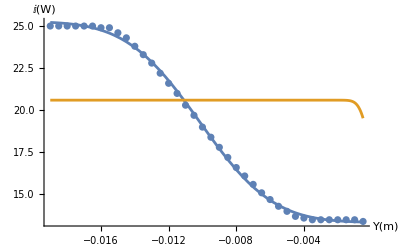

```mathematica
JumpDistance1=500*^-6;
z1=11.25*2.54*^-2+0.00000000000000000000000000001;
IIm1={13.4,13.5,13.5,13.5,13.5,13.5,13.5,13.6,13.7,14.0,14.3,14.7,15.1,15.6,16.1,16.6,17.2,17.8,18.4,19.0,19.7,20.3,21.0,21.6,22.2,22.8,23.3,23.8,24.3,24.6,24.9,24.9,25.0,25.0,25.0,25.0,25.0,25.0
};
direction=Sign[IIm1[[1]]-IIm1[[Length[IIm1]]]];
Ym1=Range[Length[IIm1]]*JumpDistance1;
Data1=Table[0,{i,2},{j,Length[IIm1]}];
Data1[[1]]=-Ym1;
Data1[[2]]=IIm1;
model=1/4 π α w^2 ( direction*erf((√2 (Y-Y0))/w)+1)+BG;
{αGuess,wGuess,Y0Guess,BGGuess}={10*(0.3/0.5)^2/(0.001^2*1/4 π),0.001,0.00002,Min[IIm1]}
modelGuess=1/4 π αGuess wGuess^2 ( direction*erf((√2 (Y-Y0Guess))/wGuess)+1)+BGGuess;
fit1=FindFit[Transpose[Data1],model,{{α,αGuess},{w,wGuess},{Y0,Y0Guess},{BG,BGGuess}},Y]
{α1,w1,Y01}={α,w,Y0}/.fit1;
Show[Plot[{model/.fit1,modelGuess},{Y,-Ym1[[1]],-Ym1[[Length[IIm1]]]},PlotRange->All,AxesLabel->{Y[m],I[W]}],ListPlot[Transpose[Data1],AxesLabel->{Y[m],I[W]}]]
```

```mathematica
(*2nd point*)
```

0.33655

{1.3751×10^8,0.0001,-0.00019,11.1}

{α→3.26355×10^7,w→0.000473871,Y0→-0.00228626,BG→11.1973}

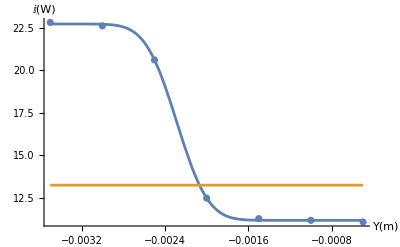

```mathematica
JumpDistance2=500*^-6;
z2=13.25*2.54*^-2+0.00000000000000000000000000001
IIm1={11.1,11.2,11.3,12.5,20.6,22.6,22.8};
direction=Sign[IIm1[[1]]-IIm1[[Length[IIm1]]]];
Ym1=Range[Length[IIm1]]*JumpDistance2;
Data1=Table[0,{i,2},{j,Length[IIm1]}];
Data1[[1]]=-Ym1;
Data1[[2]]=IIm1;
model=1/4 π α w^2 ( direction*erf((√2 (Y-Y0))/w)+1)+BG;
{αGuess,wGuess,Y0Guess,BGGuess}={3*(0.3/0.5)^2/(0.0001^2*1/4 π),0.0001,-0.00019,Min[IIm1]}
modelGuess=1/4 π αGuess wGuess^2 ( direction*erf((√2 (Y-Y0Guess))/wGuess)+1)+BGGuess;
fit1=FindFit[Transpose[Data1],model,{{α,αGuess},{w,wGuess},{Y0,Y0Guess},{BG,BGGuess}},Y]
{α2,w2,Y02}={α,w,Y0}/.fit1;
Show[Plot[{model/.fit1,modelGuess},{Y,-Ym1[[1]],-Ym1[[Length[IIm1]]]},PlotRange->All,AxesLabel->{Y[m],I[W]}],ListPlot[Transpose[Data1],AxesLabel->{Y[m],I[W]}]]
```

```mathematica
(*3rd Point*)
```

```mathematica
JumpDistance3=200*^-6;
z3=15.25*2.54*^-2+0.00000000000000000000000000001
IIm1={51.1, 50.9, 49.9, 47, 40, 29.5, 17.5, 8.49, 3.15, 0.99, 0.40, 0.21, 0.12};
direction=Sign[IIm1[[1]]-IIm1[[Length[IIm1]]]];
Ym1=Range[Length[IIm1]]*JumpDistance2;
Data1=Table[0,{i,2},{j,Length[IIm1]}];
Data1[[1]]=-Ym1;
Data1[[2]]=IIm1;
model=1/4 π α w^2 ( direction*erf((√2 (Y-Y0))/w)+1)+BG;
{αGuess,wGuess,Y0Guess,BGGuess}={3*(0.3/0.5)^2/(0.0005^2*1/4 π),0.0005,-0.00019,Min[IIm1]}
modelGuess=1/4 π αGuess wGuess^2 ( direction*erf((√2 (Y-Y0Guess))/wGuess)+1)+BGGuess;
fit1=FindFit[Transpose[Data1],model,{{α,αGuess},{w,wGuess},{Y0,Y0Guess},{BG,BGGuess}},Y]
{α3,w3,Y03}={α,w,Y0}/.fit1;
Show[Plot[{model/.fit1,modelGuess},{Y,-Ym1[[1]],-Ym1[[Length[IIm1]]]},PlotRange->All,AxesLabel->{Y[m],I[W]}],ListPlot[Transpose[Data1],AxesLabel->{Y[m],I[W]}]]
```

```mathematica
(*4th Point*)
JumpDistance4=200*^-6;
z4=17.25*2.54*^-2+0.00000000000000000000000000001
IIm1={51.5, 51.3, 50.9, 49.7, 46.8, 41.3, 33, 23.4, 14.5, 7.7, 3.43, 1.41, 0.61, 0.33, 0.18, 0.11};
direction=Sign[IIm1[[1]]-IIm1[[Length[IIm1]]]];
Ym1=Range[Length[IIm1]]*JumpDistance4;
Data1=Table[0,{i,2},{j,Length[IIm1]}];
Data1[[1]]=-Ym1;
Data1[[2]]=IIm1;
model=1/4 π α w^2 ( direction*erf((√2 (Y-Y0))/w)+1);
{αGuess,wGuess,Y0Guess}={39*(0.3/0.5)^2/(0.0005^2*1/4 π),0.0005,-0.00106}
modelGuess=1/4 π αGuess wGuess^2 ( direction*erf((√2 (Y-Y0Guess))/wGuess)+1);
fit1=FindFit[Transpose[Data1],model,{{α,αGuess},{w,wGuess},{Y0,Y0Guess}},Y]
{α4,w4,Y04}={α,w,Y0}/.fit1;
Show[Plot[{model/.fit1,modelGuess},{Y,-Ym1[[1]],-Ym1[[Length[IIm1]]]},PlotRange->All,AxesLabel->{Y[m],I[W]}],ListPlot[Transpose[Data1],AxesLabel->{Y[m],I[W]}]]
```

```mathematica
(*5th Point*)
JumpDistance5=100*^-6;
z5=10.25*2.54*^-2+0.00000000000000000000000000001
IIm1={52.2, 50.2, 44, 30.4, 13.8, 4.52, 0.73, 0.36, 0.26, 0.21, 0.19};
direction=Sign[IIm1[[1]]-IIm1[[Length[IIm1]]]];
Ym1=Range[Length[IIm1]]*JumpDistance5;
Data1=Table[0,{i,2},{j,Length[IIm1]}];
Data1[[1]]=-Ym1;
Data1[[2]]=IIm1;
model=1/4 π α w^2 ( direction*erf((√2 (Y-Y0))/w)+1);
{αGuess,wGuess,Y0Guess}={39*(0.3/0.5)^2/(0.0005^2*1/4 π),0.0005,-0.00106}
modelGuess=1/4 π αGuess wGuess^2 ( direction*erf((√2 (Y-Y0Guess))/wGuess)+1);
fit1=FindFit[Transpose[Data1],model,{{α,αGuess},{w,wGuess},{Y0,Y0Guess}},Y]
{α5,w5,Y05}={α,w,Y0}/.fit1;
Show[Plot[{model/.fit1,modelGuess},{Y,-Ym1[[1]],-Ym1[[Length[IIm1]]]},PlotRange->All,AxesLabel->{Y[m],I[W]}],ListPlot[Transpose[Data1],AxesLabel->{Y[m],I[W]}]]
```

Once we have measured the waist at multiple points, we can fit it to the beam profile to try to find the absolute waist
Equation of a focused beam waist profile: w(z)= w0*√(1+((z-z0)/z_R)^2)=w0*√(1+((z-z0)/(π*w0^2)/λ)^2) 
Where w0 is the absolute waist, z-z0 is the distance from the waist to the measurement point and λ is the wavelength

```mathematica
(*Fit points to beam profile*)
IIm1={w5, w1,w2,w3,w4}
Ym1={z5, z1,z2,z3,z4}
Data1=Table[0,{i,2},{j,Length[IIm1]}];
Data1[[1]]=Ym1;
Data1[[2]]=IIm1;
model=w0*√(1+((z-z0)/(π*w0^2)/λ)^2);
{w0Guess,z0Guess}={20*^-6,8.25*2.54*^-2}
modelGuess=w0Guess*√(1+((z-z0Guess)/zR[λ,w0Guess])^2);
fit1=FindFit[Transpose[Data1],model,{{w0,w0Guess},{z0,z0Guess}},z]
{w01,z01}={w0,z0}/.fit1;
Show[Plot[{model/.fit1,modelGuess},{z,Ym1[[1]],Ym1[[Length[IIm1]]]},PlotRange->All,AxesLabel->{Y[m],I[W]}],ListPlot[Transpose[Data1],AxesLabel->{z[m],w[m]}]]
```